```mathematica
allCrit=Map[Sort,BooleanMinimize[Reduce[
With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
]
]]];Length[allCrit]
```

32

```mathematica
vars=Sort[Map[ListofVars,ExpressionToList[Select[allCrit,Length[#]==15&]]]//Flatten//DeleteDuplicates,CompareSymbols]
```

{v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v124x35,v134x25,v135x24,v13x245,v14x235}

```mathematica
exps=Map[ListofVars,ExpressionToList[allCrit]];Length[exps]
```

544

```mathematica
CompleteGraph
```

```mathematica
Length[exps]
```

64

```mathematica
Sort[Map[{#[[1]],#[[2]]/16}&,(Flatten[exps]//Tally//Sort)/.RepGraph["C"]],#1[[2]]<#2[[2]]&]
```

{{-Graphics-296080,12},{-Graphics-317140,12},{-Graphics-317380,12},{-Graphics-361120,12},{-Graphics-361660,12},{-Graphics-295270,14},{-Graphics-295510,14},{-Graphics-296050,14},{-Graphics-317110,14},{-Graphics-360850,14},{-Graphics-295250,17},{-Graphics-295330,17},{-Graphics-295600,17},{-Graphics-296330,17},{-Graphics-297670,17},{-Graphics-297970,17},{-Graphics-302530,17},{-Graphics-303340,17},{-Graphics-319540,17},{-Graphics-319840,17},{-Graphics-360860,17},{-Graphics-361940,17},{-Graphics-368170,17},{-Graphics-368980,17},{-Graphics-382810,17},{-Graphics-383080,17},{-Graphics-492070,17},{-Graphics-492100,17},{-Graphics-514750,17},{-Graphics-514780,17}}

```mathematica
Table[Select[exps,MemberQ[#,k]&]//Length,{k,vars}]
```

{272,224,224,272,272,224,224,272,224,272,272,272,272,272,192,192,272,272,192,192,272,272,272,192,272,272,272,272,272,272}

```mathematica
triandquad=Table[allGraphs5[k,"colofour"],{k,Join[alfa1s,quads]}]
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35,v13x2x4x5,v1x24x3x5,v1x2x35x4,v14x2x3x5,v1x25x3x4}

```mathematica
reptriandquad=Table[allGraphs5[k,"colofour"]->ShowGraph5Least[k],{k,Join[alfa1s,quads]}]
```

{v13x24x5→-Graphics-361660,v14x25x3→-Graphics-317380,v1x24x35→-Graphics-296080,v13x25x4→-Graphics-361120,v14x2x35→-Graphics-317140,v13x2x4x5→-Graphics-360850,v1x24x3x5→-Graphics-296050,v1x2x35x4→-Graphics-295270,v14x2x3x5→-Graphics-317110,v1x25x3x4→-Graphics-295510}

```mathematica
Select[exps,Length[Intersection[#,triandquad]]==5&]/.reptriandquad
```

{{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,-Graphics-361660,-Graphics-361120,v14x235,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x23x4x5,-Graphics-296080,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,-Graphics-361660,-Graphics-361120,v14x23x5,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x235x4,-Graphics-296080,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,-Graphics-360850,v14x235,-Graphics-317110,v15x2x3x4,v1x23x4x5,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,-Graphics-360850,v14x23x5,-Graphics-317110,v15x2x3x4,v1x235x4,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,-Graphics-361660,-Graphics-361120,v13x2x45,v14x235,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x23x4x5,v1x245x3,-Graphics-296080,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,-Graphics-361660,-Graphics-361120,v13x2x45,v14x23x5,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x235x4,v1x245x3,-Graphics-296080,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,-Graphics-360850,v14x235,-Graphics-317110,v15x2x3x4,v1x23x4x5,v1x245x3,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,-Graphics-360850,v14x23x5,-Graphics-317110,v15x2x3x4,v1x235x4,v1x245x3,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,-Graphics-361660,-Graphics-361120,v14x235,-Graphics-317380,-Graphics-317140,v15x24x3,v1x23x4x5,-Graphics-296080,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,-Graphics-361660,-Graphics-361120,v14x23x5,-Graphics-317380,-Graphics-317140,v15x24x3,v1x235x4,-Graphics-296080,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,-Graphics-360850,v14x235,-Graphics-317110,v15x24x3,v1x23x4x5,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,-Graphics-360850,v14x23x5,-Graphics-317110,v15x24x3,v1x235x4,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,-Graphics-361660,-Graphics-361120,v13x2x45,v14x235,-Graphics-317380,-Graphics-317140,v15x24x3,v1x23x4x5,v1x245x3,-Graphics-296080,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,-Graphics-361660,-Graphics-361120,v13x2x45,v14x23x5,-Graphics-317380,-Graphics-317140,v15x24x3,v1x235x4,v1x245x3,-Graphics-296080,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,-Graphics-360850,v14x235,-Graphics-317110,v15x24x3,v1x23x4x5,v1x245x3,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,-Graphics-360850,v14x23x5,-Graphics-317110,v15x24x3,v1x235x4,v1x245x3,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,-Graphics-361660,-Graphics-361120,v14x235,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x23x4x5,-Graphics-296080,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,-Graphics-361660,-Graphics-361120,v14x23x5,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x235x4,-Graphics-296080,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,-Graphics-360850,v14x235,-Graphics-317110,v15x2x3x4,v1x23x4x5,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,-Graphics-360850,v14x23x5,-Graphics-317110,v15x2x3x4,v1x235x4,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,-Graphics-361660,-Graphics-361120,v13x2x45,v14x235,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x23x4x5,v1x245x3,-Graphics-296080,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,-Graphics-361660,-Graphics-361120,v13x2x45,v14x23x5,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x235x4,v1x245x3,-Graphics-296080,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,-Graphics-360850,v14x235,-Graphics-317110,v15x2x3x4,v1x23x4x5,v1x245x3,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,-Graphics-360850,v14x23x5,-Graphics-317110,v15x2x3x4,v1x235x4,v1x245x3,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,-Graphics-361660,-Graphics-361120,v14x235,-Graphics-317380,-Graphics-317140,v15x24x3,v1x23x4x5,-Graphics-296080,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,-Graphics-361660,-Graphics-361120,v14x23x5,-Graphics-317380,-Graphics-317140,v15x24x3,v1x235x4,-Graphics-296080,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,-Graphics-360850,v14x235,-Graphics-317110,v15x24x3,v1x23x4x5,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,-Graphics-360850,v14x23x5,-Graphics-317110,v15x24x3,v1x235x4,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,-Graphics-361660,-Graphics-361120,v13x2x45,v14x235,-Graphics-317380,-Graphics-317140,v15x24x3,v1x23x4x5,v1x245x3,-Graphics-296080,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,-Graphics-361660,-Graphics-361120,v13x2x45,v14x23x5,-Graphics-317380,-Graphics-317140,v15x24x3,v1x235x4,v1x245x3,-Graphics-296080,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,-Graphics-360850,v14x235,-Graphics-317110,v15x24x3,v1x23x4x5,v1x245x3,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,-Graphics-360850,v14x23x5,-Graphics-317110,v15x24x3,v1x235x4,v1x245x3,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,-Graphics-361660,-Graphics-361120,v14x235,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x23x4x5,-Graphics-296080,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,-Graphics-361660,-Graphics-361120,v14x23x5,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x235x4,-Graphics-296080,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,-Graphics-360850,v14x235,-Graphics-317110,v15x2x3x4,v1x23x4x5,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,-Graphics-360850,v14x23x5,-Graphics-317110,v15x2x3x4,v1x235x4,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,-Graphics-361660,-Graphics-361120,v13x2x45,v14x235,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x23x4x5,v1x245x3,-Graphics-296080,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,-Graphics-361660,-Graphics-361120,v13x2x45,v14x23x5,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x235x4,v1x245x3,-Graphics-296080,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,-Graphics-360850,v14x235,-Graphics-317110,v15x2x3x4,v1x23x4x5,v1x245x3,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,-Graphics-360850,v14x23x5,-Graphics-317110,v15x2x3x4,v1x235x4,v1x245x3,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,-Graphics-361660,-Graphics-361120,v14x235,-Graphics-317380,-Graphics-317140,v15x24x3,v1x23x4x5,-Graphics-296080,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,-Graphics-361660,-Graphics-361120,v14x23x5,-Graphics-317380,-Graphics-317140,v15x24x3,v1x235x4,-Graphics-296080,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,-Graphics-360850,v14x235,-Graphics-317110,v15x24x3,v1x23x4x5,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,-Graphics-360850,v14x23x5,-Graphics-317110,v15x24x3,v1x235x4,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,-Graphics-361660,-Graphics-361120,v13x2x45,v14x235,-Graphics-317380,-Graphics-317140,v15x24x3,v1x23x4x5,v1x245x3,-Graphics-296080,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,-Graphics-361660,-Graphics-361120,v13x2x45,v14x23x5,-Graphics-317380,-Graphics-317140,v15x24x3,v1x235x4,v1x245x3,-Graphics-296080,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,-Graphics-360850,v14x235,-Graphics-317110,v15x24x3,v1x23x4x5,v1x245x3,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,-Graphics-360850,v14x23x5,-Graphics-317110,v15x24x3,v1x235x4,v1x245x3,-Graphics-296050,-Graphics-295510,v1x2x34x5,-Graphics-295270},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,-Graphics-361660,-Graphics-361120,v14x235,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x23x4x5,-Graphics-296080,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,-Graphics-361660,-Graphics-361120,v14x23x5,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x235x4,-Graphics-296080,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,-Graphics-360850,v14x235,-Graphics-317110,v15x2x3x4,v1x23x4x5,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,-Graphics-360850,v14x23x5,-Graphics-317110,v15x2x3x4,v1x235x4,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,-Graphics-361660,-Graphics-361120,v13x2x45,v14x235,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x23x4x5,v1x245x3,-Graphics-296080,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,-Graphics-361660,-Graphics-361120,v13x2x45,v14x23x5,-Graphics-317380,-Graphics-317140,v15x2x3x4,v1x235x4,v1x245x3,-Graphics-296080,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,-Graphics-360850,v14x235,-Graphics-317110,v15x2x3x4,v1x23x4x5,v1x245x3,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,-Graphics-360850,v14x23x5,-Graphics-317110,v15x2x3x4,v1x235x4,v1x245x3,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,-Graphics-361660,-Graphics-361120,v14x235,-Graphics-317380,-Graphics-317140,v15x24x3,v1x23x4x5,-Graphics-296080,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,-Graphics-361660,-Graphics-361120,v14x23x5,-Graphics-317380,-Graphics-317140,v15x24x3,v1x235x4,-Graphics-296080,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,-Graphics-360850,v14x235,-Graphics-317110,v15x24x3,v1x23x4x5,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,-Graphics-360850,v14x23x5,-Graphics-317110,v15x24x3,v1x235x4,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,-Graphics-361660,-Graphics-361120,v13x2x45,v14x235,-Graphics-317380,-Graphics-317140,v15x24x3,v1x23x4x5,v1x245x3,-Graphics-296080,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,-Graphics-361660,-Graphics-361120,v13x2x45,v14x23x5,-Graphics-317380,-Graphics-317140,v15x24x3,v1x235x4,v1x245x3,-Graphics-296080,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,-Graphics-360850,v14x235,-Graphics-317110,v15x24x3,v1x23x4x5,v1x245x3,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,-Graphics-360850,v14x23x5,-Graphics-317110,v15x24x3,v1x235x4,v1x245x3,-Graphics-296050,v1x25x34,-Graphics-295510,-Graphics-295270}}

```mathematica
vars
```

{v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v124x35,v134x25,v135x24,v13x245,v14x235}

```mathematica
Length[exps]/32
```

17

```mathematica
edges1=Flatten[Map[Map[#[[1]]<->#[[2]]&,Subsets[#,{2}]]&,exps]];
```

```mathematica
edges=DeleteDuplicates[edges1];Length[edges]
```

405

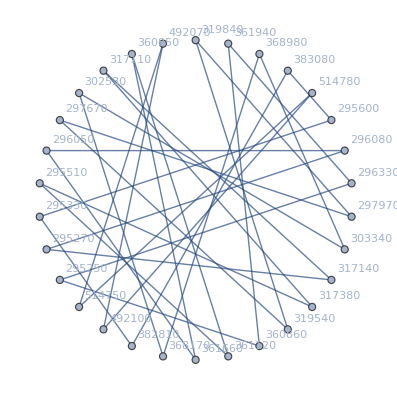

```mathematica
GraphComplement[Graph[Sort[vars,CompareSymbols],edges],GraphLayout->"CircularEmbedding",VertexLabels->Table[k->(k/.RepGraph["C"]),{k,vars}]]
```

```mathematica
MyConnect[v1_,v2_]:=If[CompareSymbols[v1,v2]<0,v1->v2,v2->v1]
```

```mathematica
MySort[s1_,s2_]:=Block[{order={v13x2x4x5,v13x24x5,v1x24x3x5,v1x24x35,v1x2x35x4,v14x2x35,v14x2x3x5,v14x25x3,v1x25x3x4,v13x25x4}},
If[MemberQ[order,s1]&&MemberQ[order,s2],
First[First[Position[order,s1]]]<First[First[Position[order,s2]]],
CompareSymbols[s1,s2]
]
]
```

```mathematica
Sort[{v13x2x4x5,v13x24x5,v13x25x4,v1x24x3x5,v1x25x3x4,v1x24x35,v14x25x3,v1x2x35x4,v14x2x3x5,v14x2x35},MySort]
```

{v13x2x4x5,v13x24x5,v1x24x3x5,v13x25x4,v1x24x35,v1x2x35x4,v14x2x35,v14x2x3x5,v14x25x3,v1x25x3x4}

```mathematica
FormulaGraphReverse2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> (SetsToSymbol[s]/.RepGraph["C"]),{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
FactorInteger[96]
```

{{2,5},{3,1}}

```mathematica
FactorInteger[128]
```

{{2,7}}

```mathematica
Sort[Subgraph[Graph[Sort[vars,CompareSymbols],edges1],{v13x2x4x5,v13x24x5,v13x25x4,v1x24x3x5,v1x25x3x4,v1x24x35,v14x25x3,v1x2x35x4,v14x2x3x5,v14x2x35}]//EdgeList//Tally,#1[[2]]<#2[[2]]&]/.RepGraph["C"]
```

{{-Graphics-317140<->-Graphics-296080,64},{-Graphics-317380<->-Graphics-317140,64},{-Graphics-361120<->-Graphics-317140,64},{-Graphics-361660<->-Graphics-317140,64},{-Graphics-360850<->-Graphics-317110,64},{-Graphics-317110<->-Graphics-296050,64},{-Graphics-360850<->-Graphics-295270,64},{-Graphics-295510<->-Graphics-295270,64},{-Graphics-317380<->-Graphics-296080,64},{-Graphics-361120<->-Graphics-317380,64},{-Graphics-361660<->-Graphics-317380,64},{-Graphics-361120<->-Graphics-296080,64},{-Graphics-361660<->-Graphics-296080,64},{-Graphics-296050<->-Graphics-295510,64},{-Graphics-361660<->-Graphics-361120,64},{-Graphics-360850<->-Graphics-317140,96},{-Graphics-317140<->-Graphics-296050,96},{-Graphics-317140<->-Graphics-295510,96},{-Graphics-317110<->-Graphics-296080,96},{-Graphics-361120<->-Graphics-317110,96},{-Graphics-361660<->-Graphics-317110,96},{-Graphics-317380<->-Graphics-295270,96},{-Graphics-361120<->-Graphics-295270,96},{-Graphics-361660<->-Graphics-295270,96},{-Graphics-360850<->-Graphics-317380,96},{-Graphics-317380<->-Graphics-296050,96},{-Graphics-360850<->-Graphics-296080,96},{-Graphics-296080<->-Graphics-295510,96},{-Graphics-361660<->-Graphics-295510,96},{-Graphics-361120<->-Graphics-296050,96},{-Graphics-317110<->-Graphics-295510,128},{-Graphics-317110<->-Graphics-295270,128},{-Graphics-296050<->-Graphics-295270,128},{-Graphics-360850<->-Graphics-295510,128},{-Graphics-360850<->-Graphics-296050,128}}

```mathematica
TriangleNumber[10]
```

55

{v13x2x4x5,v13x24x5,v13x25x4,v1x24x3x5,v1x25x3x4,v1x24x35,v14x25x3,v1x2x35x4,v14x2x3x5,v14x2x35}

{v1x2x3x45,v13x2x45,v1x245x3,v13x245}

{v1x2x34x5,v134x2x5,v1x25x34,v134x25}

{v1x23x4x5,v14x23x5,v1x235x4,v14x235}

{v15x2x3x4,v135x2x4,v15x24x3,v135x24}

{v12x3x4x5,v124x3x5,v12x35x4,v124x35}

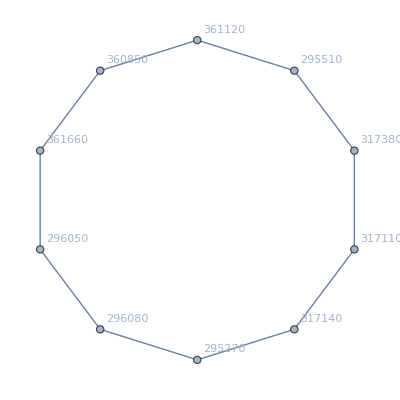
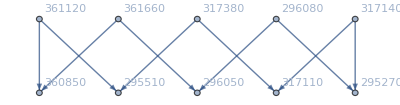
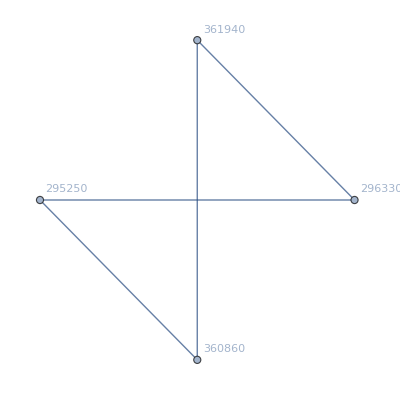
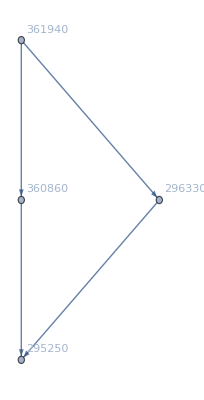
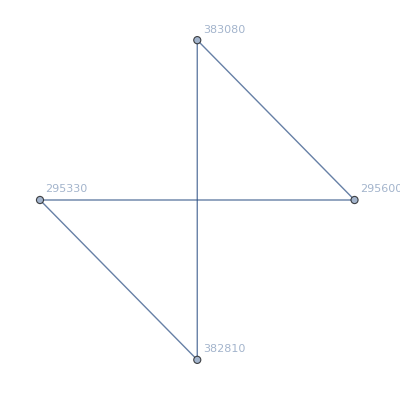
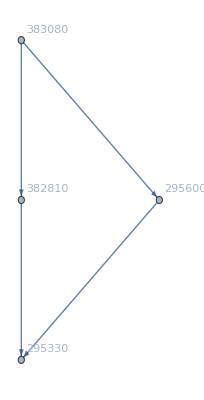
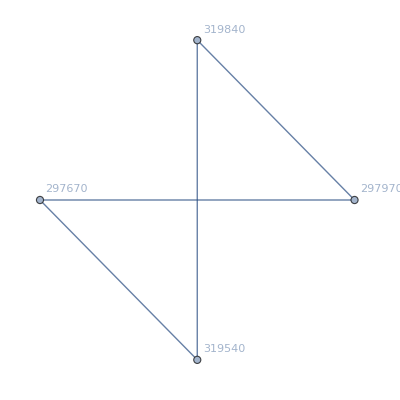
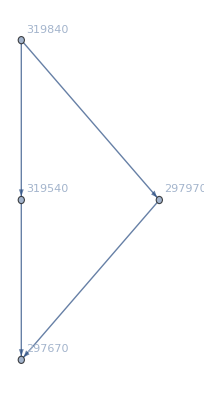

```mathematica
With[{g=GraphComplement[Graph[Sort[vars,CompareSymbols],edges],GraphLayout->"CircularEmbedding",VertexLabels->Table[k->(k/.RepGraph["C"]),{k,vars}]]},
Table[
{Graph[Subgraph[g,Sort[Print[vert];vert,MySort]],GraphLayout->"CircularEmbedding",VertexLabels->Table[k->(k/.RepGraph["C"]),{k,vars}],ImageSize->{400,400}],FormulaGraphReverse2[vert]}
,{vert,ConnectedComponents[g]}]
]
```

```mathematica
allGraphs5[29797,"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-292511--Graphics-295210--Graphics-294970--Graphics-292810+2 -Graphics-295240

```mathematica
allGraphs5[31984,"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-270643--Graphics-292511--Graphics-273340--Graphics-273100--Graphics-270941+-Graphics-295210+-Graphics-294970+-Graphics-292810+2 -Graphics-273370-2 -Graphics-295240

```mathematica
allGraphs5[31954,"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-270941--Graphics-292810--Graphics-273370+-Graphics-295240

```mathematica
allGraphs5[29767,"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-292810--Graphics-295240